## Unit Analysis

### Units using Quantity[]

```mathematica
L=Quantity[3,"Meters"]
```

3 m

```mathematica
v=Quantity[5,("Inches")/("Seconds")]
```

5 in/s

```mathematica
L/v//N
```

23.622 s

### Units using Free-form Input

Free-form input is typed using ctrl+= 
After pressing that combination of keys you should get a little box that you can type in. This box will try to interpret basic sentences or phrases and return what you asked for. For instance typing “thermal conductivity of carbon steel” returns 320. "in" ("BTU")_("IT")"/("("ft")^2"h" ("")_("Δ")^("◦")"F"")"

```mathematica
Quantity[5, ("Inches")/("Seconds")]
Quantity[320., ("Inches" "InternationalTableBritishThermalUnits")/("DegreesFahrenheitDifference" ("Feet")^2 "Hours")]
Quantity[, "SpeedOfLight"]
```

5 in/s

320. in BTU_IT/(ft^2 h _Δ^◦F)

c

```mathematica
L/Quantity[, "SpeedOfLight"]
```

3 m/c

### Using UnitConvert[]

```mathematica
UnitConvert[L/Quantity[, "SpeedOfLight"],"Seconds"]//N
```

1.00069×10^-8 s

```mathematica
UnitConvert[Quantity[6, "DegreesCelsius"],"Kelvins"]//N
```

279.15 K

```mathematica
UnitConvert[Quantity[6, "DegreesCelsiusDifference"],"KelvinsDifference"]
```

6 K

### Using QuantityMagnitude[]

```mathematica
QuantityMagnitude[L/Quantity[, "SpeedOfLight"],"Seconds"]//N
```

1.00069×10^-8

```mathematica
(*Replace all units with SI units as normal numbers*)
{Quantity[3, "Meters"],Quantity[5,"Watts"],Quantity[2, "Seconds"]}/.a_Quantity:>QuantityMagnitude[UnitConvert[a]]
```

{3,5,2}

### Independent Units

```mathematica
Quantity[2,("Hours")/IndependentUnit["Dishwasher Cycle"]]
```

2 h/Dishwasher Cycle

### What can we actually do with this?

```mathematica
UnitConvert[Quantity[2,("Hours")/IndependentUnit["Dishwasher Cycle"]]*Quantity[1,IndependentUnit["Dishwasher Cycle"]/("Weeks")]*Quantity[2000, "Watts"]*Quantity[, "Years"],"Kilowatts""Hours"]//N
```

208.571 h kW

## Symbolic Replacements

```mathematica
2 x^2+3x+1/.x->3
```

28

```mathematica
2 x^2+3x+1/.x->ⅇ^x
```

1+3 ⅇ^x+2 ⅇ^(2 x)

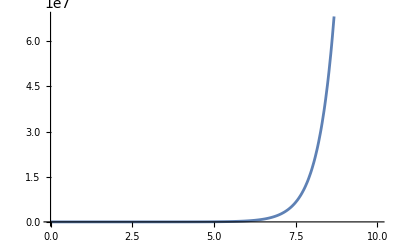

```mathematica
Plot[Evaluate[2 x^2+3x+1/.x->ⅇ^x],{x,0,10}]
```

```mathematica
D[Sin[x], x]/.x->3
```

Cos[3]

## Symbolic Simplification

### Simple simplification

```mathematica
Sin[x]^2+Cos[x]^2
```

Cos[x]^2+Sin[x]^2

```mathematica
b[x]+a[x]+c[x]
```

a[x]+b[x]+c[x]

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

### Simplification with assumptions

```mathematica
Simplify[Cos[π n]+Sin[π/2 m],Assumptions->{n∈Integers,m/2∈Integers}]
Simplify[Cos[π n]+Sin[π/2 m],Assumptions->{n∈Integers,m∈Integers,Mod[m,2]==0}]
```

(-1)^n

(-1)^n

```mathematica
Simplify[√(x^2),Assumptions->{x>0}]
```

x

### FullSimplify vs Simplify

```mathematica
Simplify[Gamma[x]x]
```

x Gamma[x]

```mathematica
FullSimplify[Gamma[x]x]
```

Gamma[1+x]

## Solve

### Solving for a single variable

```mathematica
Solve[a x^2+b x + c ==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[a0+a1 x + a2 x^2+a3 x^3 +a4 x^4+a5 x^5==0,x]
```

{{x→Root[a0+a1 #1+a2 #1^2+a3 #1^3+a4 #1^4+a5 #1^5&,1]},{x→Root[a0+a1 #1+a2 #1^2+a3 #1^3+a4 #1^4+a5 #1^5&,2]},{x→Root[a0+a1 #1+a2 #1^2+a3 #1^3+a4 #1^4+a5 #1^5&,3]},{x→Root[a0+a1 #1+a2 #1^2+a3 #1^3+a4 #1^4+a5 #1^5&,4]},{x→Root[a0+a1 #1+a2 #1^2+a3 #1^3+a4 #1^4+a5 #1^5&,5]}}

### Equations with multiple solutions

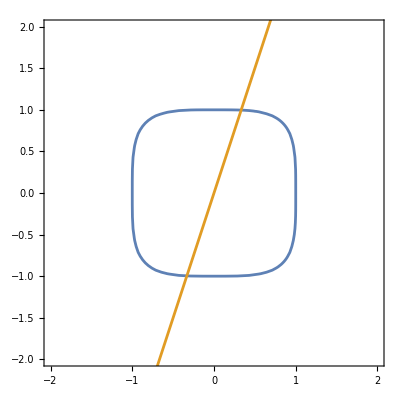

```mathematica
Show[{
ContourPlot[x^4+y^4==1,{x,-2,2},{y,-2,2}],
Plot[3x,{x,-2,2},PlotStyle->ColorData[97,2]]
}]
```

```mathematica
Solve[{
x^4+y^4==1,
y==3x
},{x,y},Reals]

sol=Solve[{
x^4+y^4==1,
y==3x
},{x,y},Assumptions->{x∈Reals,y∈Reals}]
```

{{x→-1/82^(1/4),y→-3/82^(1/4)},{x→1/82^(1/4),y→3/82^(1/4)}}

{{x→-1/82^(1/4),y→-3/82^(1/4)},{x→1/82^(1/4),y→3/82^(1/4)}}

```mathematica
{x,y}/.sol[[2]]
```

{1/82^(1/4),3/82^(1/4)}

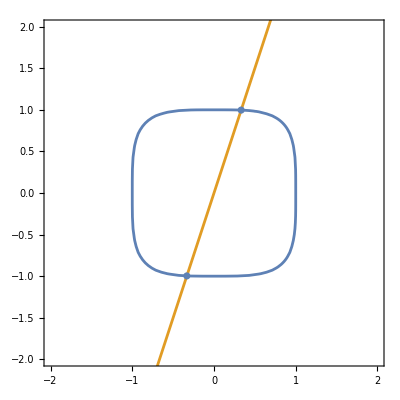

```mathematica
Show[{
ContourPlot[x^4+y^4==1,{x,-2,2},{y,-2,2}],
Plot[3x,{x,-2,2},PlotStyle->ColorData[97,2]],
ListPlot[{x,y}/.sol]
}]
```

```mathematica
Solve[{
x^4+y^4==a,
y==b x
},{x,y},Reals]
```

{{x→ConditionalExpression[-(((a b^4)/(1+b^4))^(1/4))/b, a>0],y→ConditionalExpression[-((a b^4)/(1+b^4))^(1/4), a>0]},{x→ConditionalExpression[(((a b^4)/(1+b^4))^(1/4))/b, a>0],y→ConditionalExpression[((a b^4)/(1+b^4))^(1/4), a>0]}}

```mathematica
Solve[{
x^4+y^4==a,
y==b x
},{x,y},Reals]//Normal
```

{{x→-(((a b^4)/(1+b^4))^(1/4))/b,y→-((a b^4)/(1+b^4))^(1/4)},{x→(((a b^4)/(1+b^4))^(1/4))/b,y→((a b^4)/(1+b^4))^(1/4)}}

## Other useful functions

https://reference.wolfram.com/language/tutorial/AlgebraicCalculations.html

```mathematica
Factor[2 x^2+3x+1]
```

(1+x) (1+2 x)

```mathematica
Expand[(1+x) (1+2 x)]
```

1+3 x+2 x^2

```mathematica
Apart[1/((x^2+3x+1)(3x+1)(x^2-1)x)]
```

1/(40 (-1+x))-1/x+1/(4 (1+x))+243/(8 (1+3 x))+(-123-47 x)/(5 (1+3 x+x^2))

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]